# The Mo^(..)ssbauer Effect - Experiment 28

```mathematica
<<CurveFit`
```

CurveFit for Mathematica v7.x thru v10.x, Version 1.95, 1/2016

Caltech Sophomore Physics Labs, Pasadena, CA

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

/home/yovan/Documents/Coursework/2_Smore_Year/2_Winter_2018/Ph6/Lab 6/Mossbauer_BadalYovan_2_20_2018.dat

Read 51 data points.

## Lorentzian Fit

```mathematica
LorentzianCFit[]
```

n = 51

y(ω) = c ± y_max
(γ/2)^2/(ω - ω_0)^2 +
(γ/2)^2

Fit of (x,y)  (unweighted)

y_max= 
-53.2892 | c= 
208.59 | 
σ_y_max= 
1.00673 | σ_c= 
0.721269 | 
ω_0= 
-0.20529 | γ= 
0.48465 | 
σ_ω_0= 
0.00403277 | σ_γ= 
0.0171077 | Std. deviation= 
2.13998

Fit of (x,y±σ_y)

y_max= 
-54.2411 | c= 
209.833 | 
σ_y_max= 
0.729878 | σ_c= 
0.692182 | 
ω_0= 
-0.203285 | γ= 
0.506767 | 
σ_ω_0= 
0.00257381 | σ_γ= 
0.0124181 | χ^2/(n-4)= 
1.51873

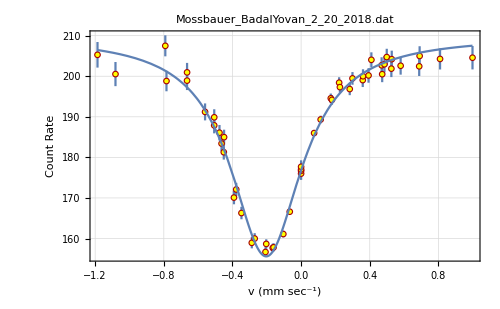
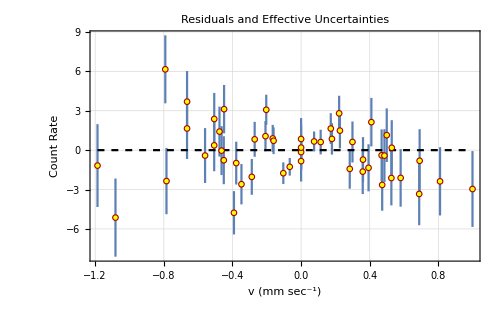
-Graphics-
-Graphics-
y(ω) = c ± y_max
(γ/2)^2/(ω - ω_0)^2 +
(γ/2)^2
y_max= 
-54.2411 | c= 
209.833 | 
σ_y_max= 
0.729878 | σ_c= 
0.692182 | 
ω_0= 
-0.203285 | γ= 
0.506767 | 
σ_ω_0= 
0.00257381 | σ_γ= 
0.0124181 | χ^2/(n-4)= 
1.51873

```mathematica
LinearDifferencePlot[FrameLabel->{"v (mm sec^-1)","Count Rate"}]
```

We observe that the data fits a Lorentzian distribution reasonably well ((χ̃)^2 of 1.52), although it seems to have higher than expected residuals around the wings of the distribution.

At the center of the line, we observe a count rate decrease of ~26 % (the Lorentzian fit gives a differential peak of -54.2 and we graphically observe a baseline of ~205). We observe a relative isomeric shift of -0.203±0.003 mm sec^-1. Therefore in accordance with our pre-lab calculations, it is more likely that the emitter is embedded in Rh (theoretical relative isomeric shift of -0.199mm sec^-1) than in Pd (theoretical relative isomeric shift of -0.186 mm sec^-1.)

According to our pre-lab calculations, we expect a FWHM of 0.193 mm sec^-1 for the Lorentzian. Instead, we observe the very different FWHM value of 0.507 mm sec^-1. This indicates that the absorption line may not be best described by a Lorentzian despite the good (χ̃)^2. One possible cause for this may be the alloying in the stainless steel, causing significant deviations from the perfect crystal structure assumptions under which our theoretical expectation was derived. Now, we expect those deviations to be independent and random throughout the crystal, which could impart a Gaussian structure to our absorption line data. Therefore, we now attempt to fit a Gaussian to our data.

## Gaussian Fit

```mathematica
(* We transform the data so we can use a Gaussian fit with an offset. *)
```

```mathematica
xnew[ x_, y_ ] := x 
ynew[ x_, y_ ] := -y 
DataTransform[]
(* Use Undo[] if you don't like the results. *)
```

All 51 points transformed.

```mathematica
GaussianCFit[]
```

n = 51

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c

Fit of (x,y)  (unweighted)

y_max= 
45.7057 | c= 
-202.699 | 
σ_y_max= 
0.774196 | σ_c= 
0.436531 | 
μ= 
-0.204306 | sigma= 
0.198951 | 
σ_μ= 
0.00334971 | σ_sigma= 
0.00446511 | Std. deviation= 
1.87357

Fit of (x,y±σ_y)

y_max= 
45.4106 | c= 
-202.199 | 
σ_y_max= 
0.572426 | σ_c= 
0.47459 | 
μ= 
-0.204099 | sigma= 
0.197143 | 
σ_μ= 
0.00249411 | σ_sigma= 
0.00351981 | χ^2/(n-4)= 
1.00177

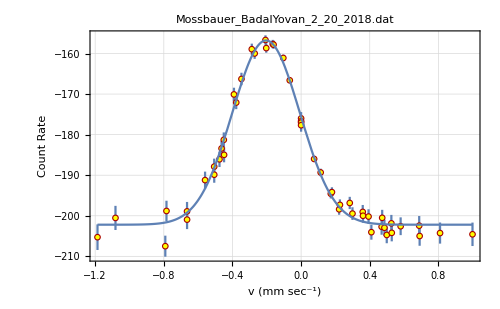
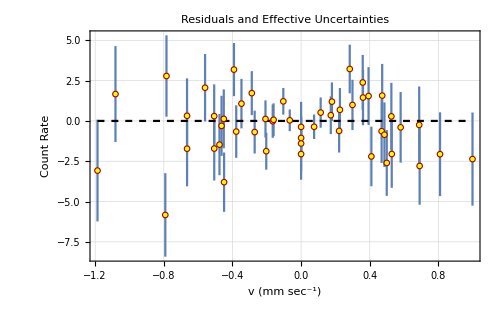
-Graphics-
-Graphics-
y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  + c
y_max= 
45.4106 | c= 
-202.199 | 
σ_y_max= 
0.572426 | σ_c= 
0.47459 | 
μ= 
-0.204099 | sigma= 
0.197143 | 
σ_μ= 
0.00249411 | σ_sigma= 
0.00351981 | χ^2/(n-4)= 
1.00177

```mathematica
LinearDifferencePlot[FrameLabel->{"v (mm sec^-1)","Count Rate"}]
```

We observe a better (χ̃)^2 for the Gaussian fit (1.002) than for the Lorentzian fit! This indicates that the alloying does in fact impart a Gaussian structure to our absorption line data. Here we obtain a FWHM of 2.36σ = 0.465±0.007 mm sec^-1. This is still much greater than our theoretical expectation (as we would expect if additional uncertainty was added to the distribution via Gaussian-distributed deviations from the theoretical distribution), but still lower than the FWHM obtained using the Lorentzian fit.

## Voigt Fit

```mathematica
Undo[]
```

Mossbauer_BadalYovan_2_20_2018.dat

n = 51

```mathematica
(* We define a scaling of the Voigt distribution with an offset and fit the PDF using FitAnyFunction.nb *)
```

```mathematica
p[fwhm_,sig_,median_,x_,k_,c_]:=k*PDF[VoigtDistribution[fwhm/2,sig],x-median]+c
```

```mathematica
FitData[
 (* The expression defining the function *) p[fwhm,sig,median,x,k,c],
(* The symbol for the variable in the expression *) x,
(* A list of the parameters in the function to fit *) {fwhm,sig ,median ,k,c},
(* A list of starting values for the parameters *) {0.15,0.1 ,-0.2 ,-30,200}
]
```

n = 51
p = 5

f[x] = c+(k (ⅇ^((fwhm/2-ⅈ (-median+x))^2/(2 sig^2)) Erfc[(fwhm/2-ⅈ (-median+x))/(√2 sig)]+ⅇ^((fwhm/2+ⅈ (-median+x))^2/(2 sig^2)) Erfc[(fwhm/2+ⅈ (-median+x))/(√2 sig)]))/(2 √(2 π) sig)

Fit of (x,y)  (unweighted):

fwhm | = | 0.198558 | ± | 0.0745072
sig | = | 0.150831 | ± | 0.0207717
median | = | -0.20488 | ± | 0.00318979
k | = | -28.872 | ± | 2.65881
c | = | 204.837 | ± | 0.979996Std. Deviation = 1.77417

Fit of (x,y±σ_y):

fwhm | = | 0.188553 | ± | 0.0789763
sig | = | 0.154429 | ± | 0.0203498
median | = | -0.204115 | ± | 0.00250897
k | = | -28.564 | ± | 2.96976
c | = | 204.6 | ± | 1.20602χ^2/(n - p) = 0.907407+0. ⅈ

{fwhm→0.188553,sig→0.154429,median→-0.204115,k→-28.564,c→204.6}

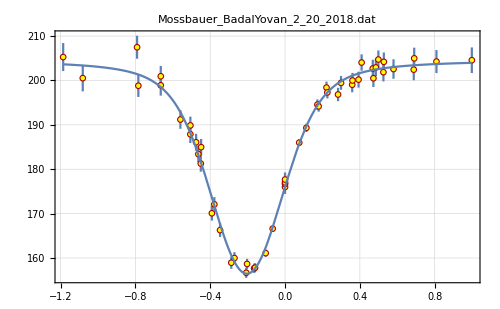

We observe that the Voigtfit is by far the best fit we have for our data, with a FWHM of 0.189±0.007 mm sec^-1 which is within error of the expected value for the FHWM. Therefore the data is most likely to be Voigt-distributed.

```mathematica
(* Note: I haven't been able to get CurveFit to plot the residuals for some reason, it simply aborts when I send the command *)
```